## Dipole v2, full |J|^2, GlobalAdaptive

```mathematica
Quit[];
```

### J2Fun

```mathematica
ClearAll[dir];
dir=FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/hong/Dipole_v2_20230201/Int

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleV2bN

```mathematica
ClearAll[DipoleV2b];
DipoleV2b=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2bN];
DipoleV2bN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2b[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### Code: DipoleSigmaN

```mathematica
ClearAll[DipoleSigma];
DipoleSigma=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{avg,avg2θk,precisiongoal,accuracygoal},

precisiongoal=6;
accuracygoal=6;

avg=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];

(*avg2θk=NIntegrate[J2CompileN[k0 Cos[θk],k0 Sin[θk],0,0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]Cos[2θk],{θk,0,2π},Method->"GlobalAdaptive"(*,WorkingPrecision->30*)(*,PrecisionGoal->precisiongoal, AccuracyGoal->accuracygoal*)];*)

avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleSigmaN];
DipoleSigmaN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleSigma[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test 1

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=0.1;
rAθ=0;
rB=0.1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

96.244493

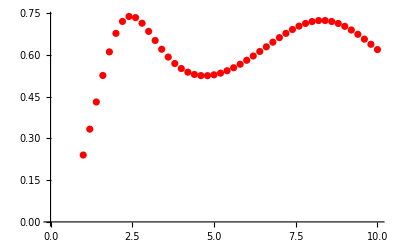

```mathematica
ListPlot[temp1,PlotStyle->Red]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

49.0466562

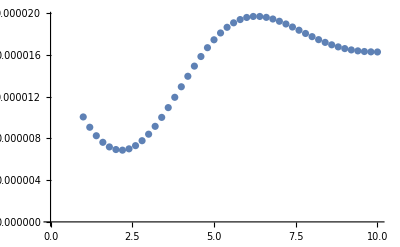

```mathematica
ListPlot[temp2]
```

### test 2

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=1;
rAθ=0;
rB=1;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

77.9518399

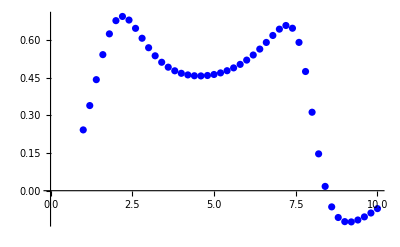

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.342785

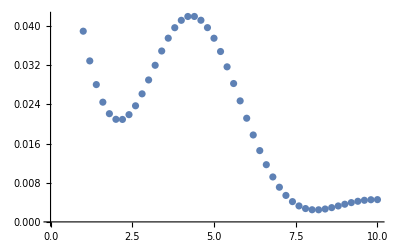

```mathematica
ListPlot[temp2]
```

### test 3

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=1;
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

```mathematica
ClearAll[ti,temp1];
ti=AbsoluteTime[];
temp1=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

98.2155183

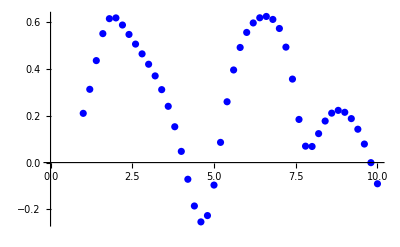

```mathematica
ListPlot[temp1,PlotStyle->Blue]
```

```mathematica
ClearAll[ti,temp2];
ti=AbsoluteTime[];
temp2=Table[{k,DipoleSigmaN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,10,0.2}]//Quiet;
AbsoluteTime[]-ti
```

28.269159

```mathematica
ListPlot[temp2]
```

-Graphics-

### b dependence for r_dp=1

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0.2;
by=0;
rA=1.0;
rAθ=π/2;
rB=1.0;
rBθ=π/2(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
ClearAll[ti,b02];
ti=AbsoluteTime[];
b02=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,30,0.2}]//Quiet;
AbsoluteTime[]-ti
$Aborted
8.714294`7.391777201428024
```

352.3954

$Aborted

8.714294

```mathematica
b02
```

{{1.,0.0199274},{1.2,0.029148},{1.4,0.0403887},{1.6,0.0538136},{1.8,0.0696026},{2.,0.0879378},{2.2,0.108978},{2.4,0.132813},{2.6,0.159386},{2.8,0.188368},{3.,0.218953},{3.2,0.249561},{3.4,0.277446},{3.6,0.298265},{3.8,0.305854},{4.,0.29269},{4.2,0.251629},{4.4,0.179053},{4.6,0.0780684},{4.8,-0.0408611},{5.,-0.163272},{5.2,-0.276003},{5.4,-0.370823},{5.6,-0.444857},{5.8,-0.498973},{6.,-0.535832},{6.2,-0.558502},{6.4,-0.569742},{6.6,-0.571737},{6.8,-0.56607},{7.,-0.553792},{7.2,-0.535509},{7.4,-0.511468},{7.6,-0.48164},{7.8,-0.445787},{8.,-0.403555},{8.2,-0.354601},{8.4,-0.298788},{8.6,-0.236501},{8.8,-0.169078},{9.,-0.0993531},{9.2,-0.0320935},{9.4,0.0260026},{9.6,0.0673232},{9.8,0.085393},{10.,0.0773342},{10.2,0.0451945},{10.4,-0.00481918},{10.6,-0.0646856},{10.8,-0.126971},{11.,-0.186194},{11.2,-0.239061},{11.4,-0.284035},{11.6,-0.32074},{11.8,-0.349445},{12.,-0.370704},{12.2,-0.385143},{12.4,-0.393341},{12.6,-0.395776},{12.8,-0.392803},{13.,-0.384654},{13.2,-0.371445},{13.4,-0.353193},{13.6,-0.329836},{13.8,-0.301261},{14.,-0.267352},{14.2,-0.228048},{14.4,-0.183435},{14.6,-0.133873},{14.8,-0.0801554},{15.,-0.0236993},{15.2,0.033284},{15.4,0.0877037},{15.6,0.135703},{15.8,0.173069},{16.,0.19596},{16.2,0.201783},{16.4,0.189911},{16.6,0.161902},{16.8,0.121105},{17.,0.0718378},{17.2,0.0184904},{17.4,-0.0351397},{17.6,-0.0861711},{17.8,-0.132667},{18.,-0.173491},{18.2,-0.208101},{18.4,-0.236348},{18.6,-0.258313},{18.8,-0.274185},{19.,-0.284191},{19.2,-0.288535},{19.4,-0.287381},{19.6,-0.280837},{19.8,-0.268958},{20.,-0.251758},{20.2,-0.22924},{20.4,-0.201433},{20.6,-0.168461},{20.8,-0.130629},{21.,-0.088542},{21.2,-0.0432536},{21.4,0.00358343},{21.6,0.0496009},{21.8,0.091707},{22.,0.126278},{22.2,0.149611},{22.4,0.158609},{22.6,0.151524},{22.8,0.128464},{23.,0.0914338},{23.2,0.0438566},{23.4,-0.0101885},{23.6,-0.0667357},{23.8,-0.122463},{24.,-0.174923},{24.2,-0.222524},{24.4,-0.264386},{24.6,-0.300142},{24.8,-0.329758},{25.,-0.353388},{25.2,-0.37127},{25.4,-0.383657},{25.6,-0.390767},{25.8,-0.39277},{26.,-0.389767},{26.2,-0.381794},{26.4,-0.368837},{26.6,-0.350849},{26.8,-0.327798},{27.,-0.299735},{27.2,-0.266897},{27.4,-0.229864},{27.6,-0.189763},{27.8,-0.148497},{28.,-0.108942},{28.2,-0.0749767},{28.4,-0.0511611},{28.6,-0.0419412},{28.8,-0.0504749},{29.,-0.0775133},{29.2,-0.12097},{29.4,-0.176434},{29.6,-0.238458},{29.8,-0.301874},{30.,-0.362663}}

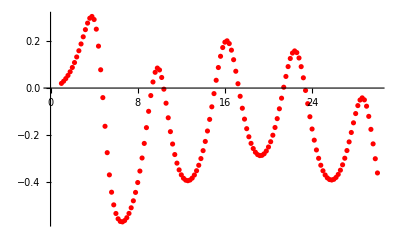

```mathematica
ListPlot[b02,PlotStyle->Red]
```

```mathematica
Getv2kT[b_]:=Module[{bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y,ti,b02},
bx=b;
by=0;
rA=1.0;
rAθ=π/2;
rB=1.0;
rBθ=π/2(*π/4*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
ClearAll[ti,b02];
ti=AbsoluteTime[];
b02=Table[{k,DipoleV2bN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},{k,1,30,0.2}]//Quiet;
Print["For b = ",b," Computation time: ",AbsoluteTime[]-ti];
Print[ListPlot[b02,PlotStyle->Red]];
b02
]
```

For b = 0.6 Computation time: 584.486553

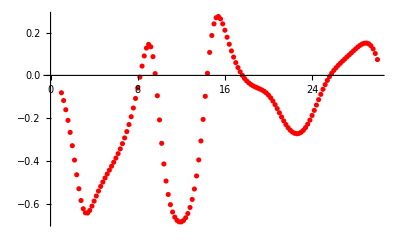

{{1.,-0.0808985},{1.2,-0.11716},{1.4,-0.160091},{1.6,-0.209659},{1.8,-0.265764},{2.,-0.32795},{2.2,-0.394857},{2.4,-0.463475},{2.6,-0.528636},{2.8,-0.58356},{3.,-0.621983},{3.2,-0.640923},{3.4,-0.641909},{3.6,-0.629676},{3.8,-0.609693},{4.,-0.586367},{4.2,-0.562492},{4.4,-0.539491},{4.6,-0.517869},{4.8,-0.497615},{5.,-0.478462},{5.2,-0.460037},{5.4,-0.441938},{5.6,-0.423763},{5.8,-0.405125},{6.,-0.385642},{6.2,-0.364939},{6.4,-0.342632},{6.6,-0.318325},{6.8,-0.291605},{7.,-0.26204},{7.2,-0.229194},{7.4,-0.192659},{7.6,-0.152119},{7.8,-0.107474},{8.,-0.0590556},{8.2,-0.00796415},{8.4,0.0434095},{8.6,0.0907826},{8.8,0.127495},{9.,0.144749},{9.2,0.133394},{9.4,0.0875138},{9.6,0.0083176},{9.8,-0.0948061},{10.,-0.207667},{10.2,-0.316766},{10.4,-0.413093},{10.6,-0.492722},{10.8,-0.555411},{11.,-0.602841},{11.2,-0.637317},{11.4,-0.661051},{11.6,-0.675841},{11.8,-0.682986},{12.,-0.683283},{12.2,-0.677057},{12.4,-0.664193},{12.6,-0.644157},{12.8,-0.616016},{13.,-0.578476},{13.2,-0.529991},{13.4,-0.468978},{13.6,-0.394253},{13.8,-0.305716},{14.,-0.205241},{14.2,-0.0975189},{14.4,0.0098161},{14.6,0.107295},{14.8,0.18603},{15.,0.240304},{15.2,0.268972},{15.4,0.27496},{15.6,0.263498},{15.8,0.240406},{16.,0.210651},{16.2,0.17809},{16.4,0.145363},{16.6,0.114133},{16.8,0.0853528},{17.,0.059483},{17.2,0.036693},{17.4,0.0169503},{17.6,0.000118996},{17.8,-0.0140091},{18.,-0.0256854},{18.2,-0.0351931},{18.4,-0.0428534},{18.6,-0.0490296},{18.8,-0.0541357},{19.,-0.0586465},{19.2,-0.0630955},{19.4,-0.06807},{19.6,-0.0741716},{19.8,-0.0819821},{20.,-0.091958},{20.2,-0.104377},{20.4,-0.119247},{20.6,-0.136284},{20.8,-0.154908},{21.,-0.174366},{21.2,-0.193782},{21.4,-0.21231},{21.6,-0.22919},{21.8,-0.243801},{22.,-0.255674},{22.2,-0.264469},{22.4,-0.269949},{22.6,-0.271942},{22.8,-0.27034},{23.,-0.265074},{23.2,-0.256132},{23.4,-0.243582},{23.6,-0.227621},{23.8,-0.208521},{24.,-0.186811},{24.2,-0.163129},{24.4,-0.13825},{24.6,-0.113033},{24.8,-0.0883113},{25.,-0.0647848},{25.2,-0.0430091},{25.4,-0.0232982},{25.6,-0.00571541},{25.8,0.00981294},{26.,0.0235291},{26.2,0.0357563},{26.4,0.0468379},{26.6,0.0571109},{26.8,0.0668933},{27.,0.0764165},{27.2,0.0858686},{27.4,0.0953541},{27.6,0.104885},{27.8,0.114382},{28.,0.123664},{28.2,0.132417},{28.4,0.140195},{28.6,0.146397},{28.8,0.150263},{29.,0.150912},{29.2,0.147351},{29.4,0.138577},{29.6,0.123713},{29.8,0.102177},{30.,0.0738465}}

```mathematica
Getv2kT[0.6]
```

```mathematica
Getv2kT[0.7]
```

```mathematica
Getv2kT[0.8]
```

```mathematica
Getv2kT[0.9]
```

```mathematica
Getv2kT[1.0]
```

```mathematica
Getv2kT[1.1]
```

```mathematica
Getv2kT[1.2]
```

```mathematica
Getv2kT[1.3]
```

```mathematica
Getv2kT[1.4]
```

```mathematica
Getv2kT[1.5]
```

```mathematica
Getv2kT[1.6]
```

```mathematica
Getv2kT[1.7]
```

```mathematica
Getv2kT[1.8]
```

```mathematica
Getv2kT[1.9]
```

```mathematica
Getv2kT[2.0]
```